#### Kuehn’s formulas

```mathematica
Σ=√0.8;
Subscript[Γ, 3][y_]:=Gamma[1+2 y/Σ^2];
Subscript[Γ, 4][y_]:=Gamma[2 y/Σ^2];
v1[y_]:=y^2;
v2[y_]:=1/2 y Σ^2;
v3[y_]:=-4^(-y/Σ^2)y(1/Σ^2)^(-2 y/Σ^2)Σ^2 Subscript[Γ, 3][y];
v4[y_]:=2^(-4 y/Σ^2)y^2(1/Σ^2)^(-4 y/Σ^2)(Subscript[Γ, 4][y])^2;
v[y_]:=v1[y]+v2[y]+v3[y]+v4[y];
m[y_]:=4^(-y/Σ^2)y(1/Σ^2)^(-2 y/Σ^2)Subscript[Γ, 4][y];
yvalues = Range[0.1,3,0.01];
theoreticalMean = ConstantArray[0,Length[yvalues]-1];
theoreticalVariance = ConstantArray[0,Length[yvalues]-1];
For[j=1,j< Length[yvalues],j++,
quot=QuotientRemainder[j,1000];
If[quot[[2]]==0,Print[j],j=j;];
Y=yvalues[[j]];
theoreticalMean[[j]]=N[m[Y]];
theoreticalVariance[[j]]=N[v[Y]];
];
Print[theoreticalMean]
Print[theoreticalVariance]
```

#### A&B definitions

```mathematica
Σ=√0.8;
Subscript[n, 1][y_]:=Gamma[2 y/Σ^2](Σ^2/2)^(2 y/Σ^2);
Subscript[n, 2][y_]:=∫_0.01^(+∞) x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2)ⅆx;
(*p[x_,y_]:=(Subscript[n, 2][y])^-1 x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);*)
p[x_,y_]:=x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
yvalues = Range[0.1,3,0.01];
FPMean = ConstantArray[0,Length[yvalues]-1];
FPVariance = ConstantArray[0,Length[yvalues]-1];
For[j=1,j< Length[yvalues],j++,
quot=QuotientRemainder[j,1000];
If[quot[[2]]==0,Print[j],j=j;];
Y=yvalues[[j]];
FPMean[[j]]=NIntegrate[x p[x,Y],{x,0,+∞},Method->{"LocalAdaptive"}];
FPVariance[[j]]=NIntegrate[(x-FPMean[[j]])^2 p[x,Y],{x,0,+∞},Method->{"LocalAdaptive"}];;
];
(*Print[FPMean]*)
Print[FPVariance]
```

{0.217572,0.186027,0.162075,0.143696,0.129479,0.118416,0.109772,0.103004,0.0977033,0.0935603,0.0903363,0.0878464,0.0859457,0.0845202,0.0834795,0.0827516,0.0822784,0.0820136,0.0819194,0.0819655,0.0821269,0.0823835,0.0827189,0.0831195,0.0835744,0.0840746,0.0846126,0.0851827,0.0857797,0.0863999,0.08704,0.0876974,0.0883702,0.0890567,0.0897556,0.0904662,0.0911876,0.0919194,0.0926612,0.0934131,0.0941749,0.0949466,0.0957285,0.0965207,0.0973237,0.0981375,0.0989628,0.0997998,0.100649,0.101511,0.102386,0.103274,0.104177,0.105094,0.106026,0.106974,0.107939,0.10892,0.109918,0.110934,0.111969,0.113022,0.114095,0.115189,0.116303,0.117438,0.118595,0.119774,0.120977,0.122203,0.123453,0.124729,0.12603,0.127357,0.12871,0.130092,0.131501,0.132939,0.134406,0.135904,0.137432,0.138992,0.140584,0.142209,0.143868,0.145561,0.147289,0.149054,0.150855,0.152694,0.154571,0.156487,0.158444,0.160441,0.16248,0.164563,0.166688,0.168859,0.171075,0.173337,0.175647,0.178006,0.180414,0.182873,0.185383,0.187946,0.190563,0.193236,0.195964,0.19875,0.201594,0.204498,0.207463,0.21049,0.213581,0.216737,0.219959,0.223249,0.226607,0.230036,0.233537,0.237111,0.24076,0.244485,0.248288,0.25217,0.256133,0.260178,0.264308,0.268523,0.272826,0.277218,0.281701,0.286277,0.290947,0.295713,0.300577,0.30554,0.310606,0.315774,0.321048,0.32643,0.33192,0.337521,0.343236,0.349065,0.355011,0.361075,0.367261,0.373569,0.380001,0.38656,0.393247,0.400065,0.407015,0.414099,0.421318,0.428676,0.436172,0.443811,0.451592,0.459517,0.467589,0.475808,0.484177,0.492696,0.501367,0.510191,0.519169,0.528302,0.537591,0.547037,0.55664,0.566401,0.57632,0.586396,0.596631,0.607024,0.617573,0.628279,0.63914,0.650156,0.661323,0.672641,0.684107,0.695718,0.707472,0.719365,0.731393,0.743552,0.755838,0.768244,0.780766,0.793396,0.806128,0.818954,0.831867,0.844856,0.857913,0.871026,0.884186,0.897379,0.910593,0.923814,0.937027,0.950217,0.963367,0.976459,0.989474,1.00239,1.01519,1.02786,1.04035,1.05266,1.06476,1.07662,1.08821,1.0995,1.11046,1.12106,1.13127,1.14105,1.15037,1.15919,1.16747,1.17519,1.1823,1.18875,1.19453,1.19957,1.20386,1.20735,1.21,1.21179,1.21268,1.21264,1.21165,1.20968,1.20673,1.20278,1.19782,1.19188,1.18496,1.17709,1.16832,1.1587,1.14832,1.13726,1.12566,1.11366,1.10143,1.0892,1.07722,1.06577,1.05522,1.04597,1.03848,1.0333,1.03104,1.03241,1.03823,1.04941,1.06701,1.09222,1.12638,1.17102,1.22785,1.29881,1.38609,1.49213,1.61968,1.77185,1.95207,2.16425,2.4127,2.70229,3.03843,3.42717,3.87528,4.39027,4.98056,5.6555,6.42551,7.3022,8.29846,9.42868,10.7088,12.1566,13.7919,15.6364}

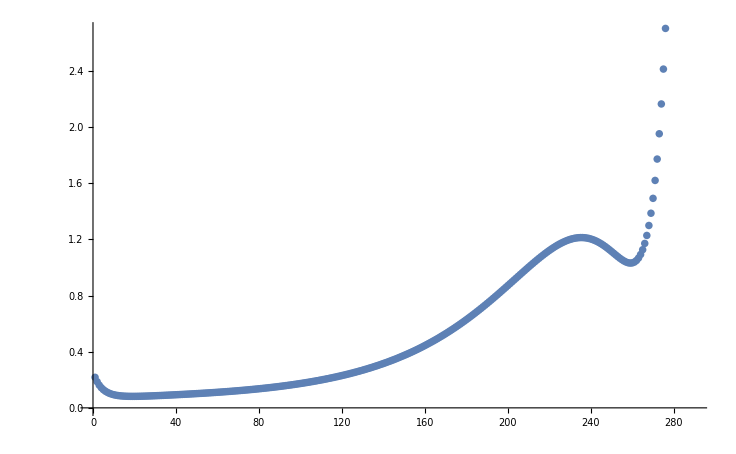

```mathematica
ListPlot[FPVariance]
```

#### F-P distribution @ fixed y-values

```mathematica
Subscript[n, 2][y_]:=(∫_0.01^(+∞) x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2)ⅆx)^-1;
p[x_,y_]:=Subscript[n, 2][y] x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
yvaluesNew = List[0.39292,0.68585,0.97878,1.27127,1.56464,1.85757,2.15050,2.44343];
xvalues = Range[0.01,6,0.1];
distro = ConstantArray[0,Length[xvalues]-1];
For[j=1,j< Length[yvaluesNew],j++,
Y=yvaluesNew[[j]];
distro = ConstantArray[0,Length[xvalues]-1];
For[k=1,k< Length[xvalues],k++,
X=xvalues[[k]];
distro[[k]]=N[p[X,Y]];
];
Print[distro]
];
```

#### Normalization constant

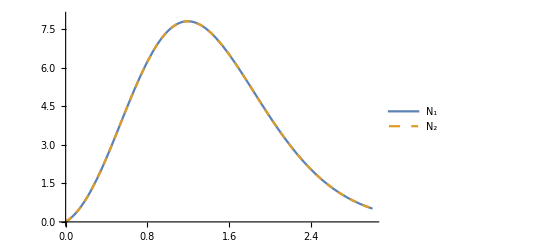

```mathematica
Σ=√0.8;
Subscript[n, 1][y_]:=Gamma[2 y/Σ^2](Σ^2/2)^(2 y/Σ^2);
f[x_,y_]:=x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
Subscript[n, 2][y_]:=NIntegrate[f[x,y],{x,0,+∞},Method->{"LocalAdaptive","SingularityHandler"-> "DoubleExponential"},PrecisionGoal->10, Exclusions->{0}];
Plot[{(Subscript[n, 1][y])^-1,(Subscript[n, 2][y])^-1},{y,0,3},PlotRange->{0, 8},PlotLegends->{"N_1","N_2"}, PlotStyle->{Thick,Dashed}]
```

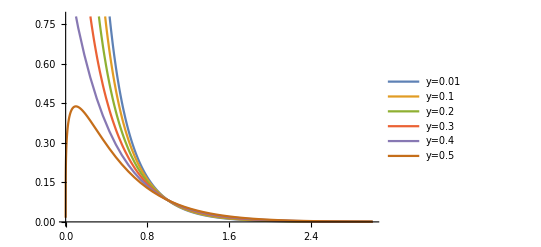

```mathematica
(*https://reference.wolfram.com/language/tutorial/NIntegrateIntegrationStrategies.html*)
Y=0.1;
f[x_,y_]:=x^(2 y/Σ^2-1)ⅇ^(-2 x/Σ^2);
g[x_]:=f[x,Y];
Plot[{f[x,0.01],f[x,0.1],f[x,0.2],f[x,0.3], f[x,0.4], f[x,0.5]},{x,0,3},PlotLegends->{"y=0.01", "y=0.1", "y=0.2", "y=0.3", "y=0.4", "y=0.5"}]
```